```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]]
```

/home/elio/MEGA/gravEoS/JL

```mathematica
outputVideoName = "None" ;
```

```mathematica
prms = Import["OUTPUT/PARAMS.dat"];
m = prms[[1,1]]; r = prms[[1,2]];
xi = prms[[2,1]]; xf = prms[[2,2]];
yi = prms[[3,1]]; yf = prms[[3,2]];
zi = prms[[4,1]]; zf = prms[[4,2]];
nbp = prms[[5,1]]; lns = prms[[5,2]]; ;
```

```mathematica
qqq = ConstantArray[0,{nbp,lns,5}];
For[i=1, i<=nbp, i++,
qqq[[i]]=Import[StringJoin["OUTPUT/particle",ToString[i],".dat"]];
]
```

```mathematica
Print[Style[Dimensions[qqq][[2]],20,Red]]
```

3001

```mathematica
maxKinE = Max[qqq[[;;,;;,5]]];
{Round[maxKinE,1],maxKinE}
```

{18,18.1371}

```mathematica
kinColor=ColorData["DarkRainbow"];
(*anm=Animate[
Canvas[
Graphics3D[Table[{kinColor[qqq[[i,st,5]]/Round[maxKinE,1]],Sphere[qqq[[i,st,2;;4]],r]},{i,1,nbp,1}],PlotRange->{{xi,xf},{yi,yf},{zi,zf}},ImageSize->600],
BarLegend[{"DarkRainbow",{0,Round[maxKinE,100]}},LegendLabel->"E_kin",LabelStyle->Directive[Black,FontSize->18]]
],
{st,1,Dimensions[qqq][[2]],1},ContinuousAction->False,DefaultDuration->60]*)
```

```mathematica
(*Export["tst.mp4",anm,ImageSize->{1920,1080},Antialiasing->True,CompressionLevel->0,DefaultDuration->60]*)
```

```mathematica
diamN2=0.32 10^-9;
volN2 = (4π)/3(diamN2/2)^3;
nAirSC=1.204/(4.81 10^-26);
nAirSC volN2 //ScientificForm
```

4.29467×10^-4

```mathematica
(nbp(4π)/3 r^3)/(Abs[zi-zf]Abs[yi-yf]Abs[yi-yf])//ScientificForm
```

6.6268×10^-3

```mathematica
mnpl=Manipulate[
Canvas[
Graphics3D[Table[{kinColor[qqq[[i,st,5]]/maxKinE],Sphere[qqq[[i,st,2;;4]],r]},{i,1,nbp,1}],PlotRange->{{xi,xf},{yi,yf},{zi,zf}},ImageSize->600],
BarLegend[{"DarkRainbow",{0,Round[maxKinE,100]}},LegendLabel->"E_kin",LabelStyle->Directive[Black,FontSize->18]]
],
{st,1,Dimensions[qqq][[2]],1},
ContinuousAction->False,AutorunSequencing->0]
```

```mathematica
(*Export["mnpl.mp4",mnpl,ImageSize->{1920,1080},CompressionLevel->0,DefaultDuration->60]*)
```

```mathematica
If[outputVideoName!="None",

For[st=1,st<=Dimensions[qqq][[2]],st++,
Export[StringJoin["pics/st",IntegerString[st,10,4],".png"],
Rasterize[Canvas[
Graphics3D[Table[{kinColor[qqq[[i,st,5]]/Round[maxKinE,1]],Sphere[qqq[[i,st,2;;4]],r]},{i,1,nbp,1}],PlotRange->{{xi,xf},{yi,yf},{zi,zf}},ImageSize->600],
BarLegend[{"DarkRainbow",{0,Round[maxKinE,100]}},LegendLabel->"E_kin",LabelStyle->Directive[Black,FontSize->18]]
],ImageSize->400,ImageResolution->66]
]
];

Run[StringJoin["ffmpeg -y -framerate 10 -pattern_type glob -i 'pics/*.png' -c:v mpeg4 -q:v 2 ",outputVideoName,".avi"]];
Run["rm -r pics/*.png "];

]
```

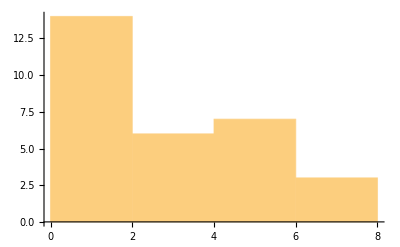

```mathematica
Histogram[qqq[[;;,Dimensions[qqq][[2]],5]]]
```

```mathematica
Dimensions[qqq[[;;,1,5]]]
```

{30}